## OutwardNormalVector-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m;
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 13:10:30
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
```

```mathematica
vecs=OutwardNormalVector[polygon, #]&/@Range[Length[polygon]]
```

{{-0.132015,0.991248},{-0.508225,0.861224},{-0.69443,0.71956},{-0.528603,-0.848869},{0.816372,-0.577527},{0.444089,-0.895983},{0.840309,-0.542108}}

```mathematica
midpoints=MidPoint[polygon]
```

{{0.516554,0.568653},{-0.0704379,0.2904},{-0.735411,-0.187169},{-0.783232,-0.51799},{-0.448916,-0.41049},{0.0416231,-0.0250531},{0.521407,0.364877}}

```mathematica
arrows=Arrow/@Transpose[{midpoints, midpoints+vecs}]
```

{Arrow[{{0.516554,0.568653},{0.384539,1.5599}}],Arrow[{{-0.0704379,0.2904},{-0.578663,1.15162}}],Arrow[{{-0.735411,-0.187169},{-1.42984,0.532391}}],Arrow[{{-0.783232,-0.51799},{-1.31183,-1.36686}}],Arrow[{{-0.448916,-0.41049},{0.367456,-0.988017}}],Arrow[{{0.0416231,-0.0250531},{0.485712,-0.921036}}],Arrow[{{0.521407,0.364877},{1.36172,-0.177231}}]}

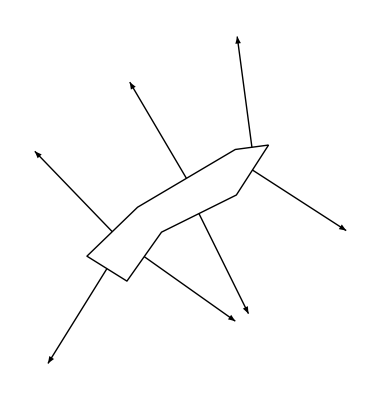

```mathematica
Show[Boundary[polygon], Graphics[arrows]]
```

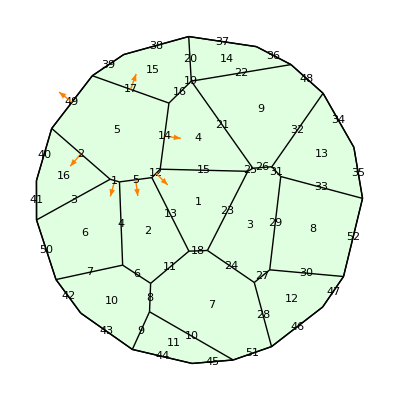

```mathematica
w=TemplateRandomCircularGrid[16,10];
Show[ShowTissue[w,"CellNumbers"->True,"EdgeNumbers"->True],ShowOutwardNormals[CellVertexCoordinates[w,5], Orange]]
```

```mathematica
OutwardNormalVector[w,5]
```

{{-0.7921,0.610391},{-0.656048,-0.754719},{-0.271868,-0.962335},{0.130538,-0.991443},{0.712416,-0.701758},{0.991309,-0.131551},{0.336317,0.941749}}

```mathematica
OutwardNormalVector[w,5,3]
```

{-0.271868,-0.962335}